```mathematica
transformation = LinearFractionalTransform[{{a,b,c},{e,f,g},{h,i,j}}]
PNEW = {(a x + b y + c)/(h x + i y + j),(e x + f y + g)/(h x + i y + j)}
```

TransformationFunction[(a | b | c
e | f | g
h | i | j)]

{(c+a x+b y)/(j+h x+i y),(g+e x+f y)/(j+h x+i y)}

Polygon[…]

{{-0.576396,0.530999},{-0.568677,0.560406},{-0.552124,0.382736},{-0.526283,0.332269},{-0.512422,0.708676},{-0.443372,0.227614},{-0.292566,0.0426392},{-0.180285,0.822149},{0.,0.},{0.126355,0.0106049},{0.280476,0.129518},{0.296263,0.188555},{0.3593,0.457976},{0.393145,0.629058},{0.393153,0.826614}}

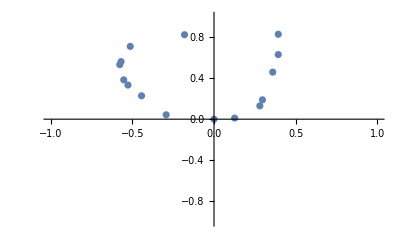

```mathematica
Poly = RandomPolygon["Convex"]
Shape = PolygonCoordinates[Poly]
ListPlot[Shape, PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
Newshape = transformation[Shape]
```

{{(-0.576396 a+0.530999 b+c)/(-0.576396 h+0.530999 i+j),(-0.576396 e+0.530999 f+g)/(-0.576396 h+0.530999 i+j)},{(-0.568677 a+0.560406 b+c)/(-0.568677 h+0.560406 i+j),(-0.568677 e+0.560406 f+g)/(-0.568677 h+0.560406 i+j)},{(-0.552124 a+0.382736 b+c)/(-0.552124 h+0.382736 i+j),(-0.552124 e+0.382736 f+g)/(-0.552124 h+0.382736 i+j)},{(-0.526283 a+0.332269 b+c)/(-0.526283 h+0.332269 i+j),(-0.526283 e+0.332269 f+g)/(-0.526283 h+0.332269 i+j)},{(-0.512422 a+0.708676 b+c)/(-0.512422 h+0.708676 i+j),(-0.512422 e+0.708676 f+g)/(-0.512422 h+0.708676 i+j)},{(-0.443372 a+0.227614 b+c)/(-0.443372 h+0.227614 i+j),(-0.443372 e+0.227614 f+g)/(-0.443372 h+0.227614 i+j)},{(-0.292566 a+0.0426392 b+c)/(-0.292566 h+0.0426392 i+j),(-0.292566 e+0.0426392 f+g)/(-0.292566 h+0.0426392 i+j)},{(-0.180285 a+0.822149 b+c)/(-0.180285 h+0.822149 i+j),(-0.180285 e+0.822149 f+g)/(-0.180285 h+0.822149 i+j)},{c/j,g/j},{(0.126355 a+0.0106049 b+c)/(0.126355 h+0.0106049 i+j),(0.126355 e+0.0106049 f+g)/(0.126355 h+0.0106049 i+j)},{(0.280476 a+0.129518 b+c)/(0.280476 h+0.129518 i+j),(0.280476 e+0.129518 f+g)/(0.280476 h+0.129518 i+j)},{(0.296263 a+0.188555 b+c)/(0.296263 h+0.188555 i+j),(0.296263 e+0.188555 f+g)/(0.296263 h+0.188555 i+j)},{(0.3593 a+0.457976 b+c)/(0.3593 h+0.457976 i+j),(0.3593 e+0.457976 f+g)/(0.3593 h+0.457976 i+j)},{(0.393145 a+0.629058 b+c)/(0.393145 h+0.629058 i+j),(0.393145 e+0.629058 f+g)/(0.393145 h+0.629058 i+j)},{(0.393153 a+0.826614 b+c)/(0.393153 h+0.826614 i+j),(0.393153 e+0.826614 f+g)/(0.393153 h+0.826614 i+j)}}

```mathematica
lower = -5
upper = 5
Manipulate[ListPlot[Newshape/.{a->p,b->q,c->r,e->t,f->u,g->v,h->w,i->z, j -> o},PlotRange->{{-1,1},{-1,1}}],{{p,1},lower,upper}, {{q,0},lower,upper}, {{r,0},lower,upper},{{t,0},lower,upper}, {{u,1},lower,upper}, {{v,0},lower,upper}, {{w,0},lower,upper}, {{z,0},lower,upper}, {{o,1},lower,upper}]
```

-5

5